## 134Ce

```mathematica
ClearAll["Global`*"]
```

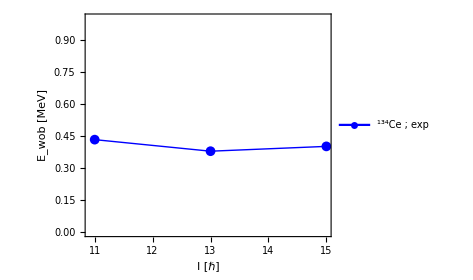

```mathematica
yrastEn=Sort[{8583,7581,6597,5724,4907,4183,3719}];
wob1En=Sort[{5717,4924,4384}];
yrastSpin=Table[i,{i,10,16,2}];
wob1Spin=Table[i,{i,11,15,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","134"],"Ce ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/134Ce.pdf",fig];
Show[fig]
```